```mathematica
Module[{list,dist},
list={{1.5,0.6},{2,0},{1.25,1.25}};
dist[{u_,v_}, {x_,y_}] := 3Abs[u-x]+2Abs[v-y];
Nearest[list,{0,0},DistanceFunction->dist]
]
```

{{1.5,0.6}}

```mathematica
Manipulate[
Module[{Tcmix,Pcmix,Psat1,Psat2,Px,Py,dist,near,pos,Pxnew},
Tcmix:=-13.795*x^2-41.45*x+424.94;
Pcmix:=-4.8074*x^3-0.2772*x^2+9.6962*x+37.963;

Psat1[T_]:=10^(4.53678-1149.36/(T+24.906));
Psat2[T_]:=10^(4.35576-1175.581/(T-2.071));

Px:=Table[{T,x*Psat1[T]+(1-x)*Psat2[T]},{T,346,Tcmix}];
Py:=Table[{T,(x/Psat1[T]+(1-x)/Psat2[T])^-1},{T,346,Tcmix}];

dist[{u_,v_},{a_,b_}]:=Abs[v-b];
near:=Nearest[Px,{Tcmix,Pcmix},2,DistanceFunction->dist];
pos:=Position[Px,If[near[[1,2]]>near[[2,2]],First@near,Last@near]][[1,1]];

Pxnew:=Interpolation[Insert[Drop[Px,-(Length[Px]-pos)],{Pcmix,Tcmix},pos+1]];

Plot[Pxnew[T],{T,346,Tcmix}]

],
Control[{{x,0.1,"propane mole fraction"},0,1,0.1,Appearance->"Labeled"}]
]
```

```mathematica
Manipulate[
Module[{Tc1,Tc2,Tcmix,Pcmix,Psat1,Psat2,Px,Py,data,dist,near,pos,newdata,plot},
Tc1=369.8;Tc2=425.2;(*K*)

Tcmix:=-13.795*x^2-41.45*x+424.94;
Pcmix:=-4.8074*x^3-0.2772*x^2+9.6962*x+37.963;

Psat1[T_]:=10^(4.53678-1149.36/(T+24.906));
Psat2[T_]:=10^(4.35576-1175.581/(T-2.071));

Px[T_]:=x*Psat1[T]+(1-x)*Psat2[T];
Py[T_]:=(x/Psat1[T]+(1-x)/Psat2[T])^-1;

data[func_]:=Table[{T,func},{T,346,Tcmix}];
dist[{u_,v_},{a_,b_}]:=Abs[v-b];
near[func_]:=Nearest[data[func],{Tcmix,Pcmix},2,DistanceFunction->dist];
pos[func_]:=Position[data[func],If[near[func][[1,2]]>near[func][[2,2]],First@near[func],Last@near[func]]][[1,1]];

(*newdata[func_]:=Quiet@Interpolation[Insert[Drop[data[func],-(Length[data[func]]-pos[func])],{Tcmix,Pcmix},pos[func]+1],InterpolationOrder->IO][T];*)
(*newdata[func_]:=Insert[Drop[data[func],-(Length[data[func]]-pos[func])],{Tcmix,Pcmix},pos[func]+1];*)

newdata[func_,i_]:=Insert[Insert[Drop[data[func],-(Length[data[func]]-pos[func])],{0.5*(Tcmix+First@data[func][[pos[func]]]),0.5*(Pcmix+Last@data[func][[pos[func]+2*i]])},pos[func]+1],{Tcmix,Pcmix},pos[func]+2];

(*newdata[func_]:=Insert[Insert[Drop[data[func],-(Length[data[func]]-pos[func])],{0.5*(Tcmix+First@data[func][[pos[func]]]),Last@data[func][[pos[func]]]},pos[func]+1],{Tcmix,Pcmix},pos[func]+2];*)

Show[
Plot[Psat1[T],{T,346,Tc1},PlotStyle->{Thick,Black}],
Plot[Psat2[T],{T,363,Tc2},PlotStyle->{Thick,Black}],

ListPlot[{newdata[Px[T],1],newdata[Py[T],-1]},Joined->True,PlotStyle->{{Thick,Blue},{Thick,Green}}],
(*Graphics[{PointSize[0.01],
Point[{0.5*(Tcmix+First@data[Px[T]][[pos[Px[T]]]]),0.5*(Pcmix+Last@data[Px[T]][[pos[Px[T]]+2]])}],Point[{0.5*(Tcmix+First@data[Py[T]][[pos[Py[T]]]]),0.5*(Pcmix+Last@data[Py[T]][[pos[Py[T]]-2]])}]
(*Point[{0.5*(Tcmix+First@data[Px[T]][[pos[Px[T]]]]),Last@data[Px[T]][[pos[Px[T]]]]}],Point[{0.5*(Tcmix+First@data[Py[T]][[pos[Py[T]]]]),Last@data[Py[T]][[pos[Py[T]]]]}]*)
(*Point[{0.5*(Tcmix+First@data[Px[T]][[pos[Px[T]]]]),0.5*(Pcmix+Last@data[Px[T]][[pos[Px[T]]]])}],Point[{0.5*(Tcmix+First@data[Py[T]][[pos[Py[T]]]]),0.5*(Pcmix+Last@data[Py[T]][[pos[Py[T]]]])}]*)
}],*)
(*Plot[{Quiet@Interpolation[newdata[Px[T],1],InterpolationOrder->IO][T],Quiet@Interpolation[newdata[Py[T],-1],InterpolationOrder->IO][T]},{T,346,Tcmix},PlotStyle->{{Thick,Blue},{Thick,Green}}],*)

Axes->False,Frame->True,FrameLabel->{Style["temperature (K)",17],Style["pressure  (bar)",17]},LabelStyle->{Black,14},ImageSize->{550,400},PlotRange->{{345,425},{12,45}},ImagePadding->{{45,5},{45,10}},PlotLabel->Style[Row[{"propane - ",Style["n",Italic],"-butane"}],17]]
(*{Tcmix,First@data[Py[T]][[pos[Py[T]]]],0.5*(Tcmix+First@data[Py[T]][[pos[Py[T]]]])}*)

],
Control[{{IO,2,""},0,6,1,Appearance->"Labeled"}],
Control[{{x,0.1,"propane mole fraction"},0,1,0.1,Appearance->"Labeled"}]
]
```

```mathematica
Insert[Insert[{{1,a},{2,b},{3,c}},{4,c},4],{5,d},5]
```

{{1,a},{2,b},{3,c},{4,c},{5,d}}

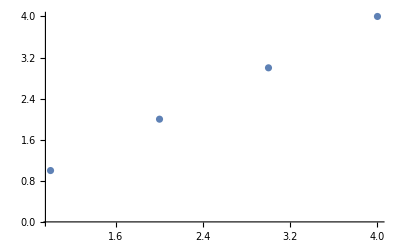

```mathematica
ListPlot[Insert[{{1,1},{2,2},{3,3}},{4,4},4]]
```

```mathematica
0.5*{1+3,1+1}
```

{2.,1.}

```mathematica
Manipulate[
Module[{Tcmix,Pcmix,Psat1,Psat2,Px,Py},
Tcmix:=-13.795*x^2-41.45*x+424.94;
Pcmix:=-4.8074*x^3-0.2772*x^2+9.6962*x+37.963;

Psat1:=10^(4.53678-1149.36/(T+24.906));
Psat2:=10^(4.35576-1175.581/(T-2.071));

Px:=x*Psat1+(1-x)*Psat2;
Py:=(x/Psat1+(1-x)/Psat2)^-1;

Plot[{Px,Py},{x,0,1}]
],
Control[{{T,350,"T"},300,425,1,Appearance->"Labeled"}]
]
```

```mathematica
Table[-13.795*x^2-41.45*x+424.94,{x,{0,1}}]
```

{424.94,369.695}